## Impedanz eines Serien Schwingkreises

```mathematica
Clear[z1, z2];
```

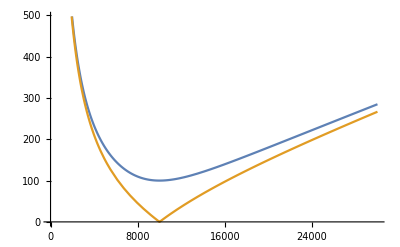

```mathematica
z1[ω_]:=100+ⅈ*(ω*0.01-1/(ω*0.000001)) (*With Resistance*)
z2[ω_]:=ⅈ*(ω*0.01-1/(ω*0.000001)) (*No Resistance*)
Plot[{Abs[z1[ω]], Abs[z2[ω]]},{ω,0,30000}]
```

## Resonanzkreisfrequenz

```mathematica
NMinimize[Abs[z1[ω]], ω]
```

{100.,{ω→-10000.}}

## Ortskurve

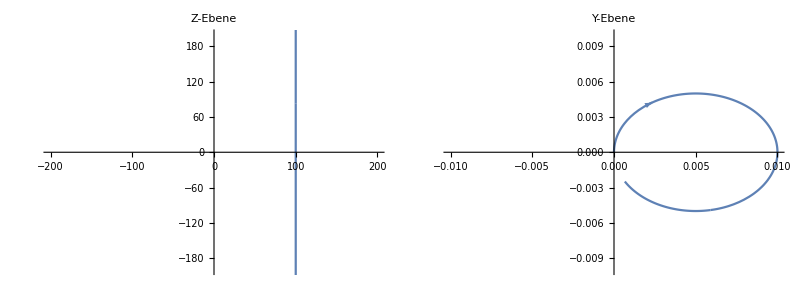

```mathematica
ok1=NyquistPlot[z1[ω], {ω, 1, 40000}, PlotRange->200, ImageSize->Medium, PlotLabel->"Z-Ebene"];
ok2= NyquistPlot[1/z1[ω], {ω, 1, 40000}, PlotRange->0.01, ImageSize->Medium, PlotLabel->"Y-Ebene"];
Grid[{{ok1, ok2}}]
```